```mathematica
data=Transpose[Import["C:\\Users\\Abigail\\Desktop\\Wolfram data\\Nematode\\Clade five\\Mt genes\\Nematode clade five-mt genes.csv"]];
Dimensions[data]
```

{7,106}

```mathematica
nematode12S=data[[2,2;;106]]
nematode16S=data[[3,2;;106]]
nematodeCOI=data[[4,2;;106]]
nematodeCOII=data[[5,2;;106]]
nematodecytb=data[[6,2;;106]]
nematodeND=data[[7,2;;106]]
```

{0.046,0.072,0.043,0.058,0.078,0.086,0.066,0.014,0.006,0.009,0.026,0.032,0.11,0.115,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.161,0.156,0.164,0.17,0.135,0.13,0.127,0.124,0.124,0.141,0.127,0.127,0.176,0.164,0.184,0.173,0.147,0.135,0.133,0.13,0.13,0.147,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.069,0.086,0.095,0.086,0.066,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.141,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.066,0.075,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}

{0.065,0.116,0.075,0.127,0.108,0.113,0.109,0.066,0.018,0.056,0.096,0.041,0.164,0.162,0.111,0.116,0.106,0.089,0.101,0.098,0.104,0.182,0.175,0.175,0.19,0.164,0.141,0.157,0.142,0.159,0.159,0.157,0.164,0.184,0.164,0.172,0.189,0.164,0.149,0.151,0.149,0.161,0.167,0.161,0.167,0.172,0.167,0.174,0.162,0.18,0.162,0.124,0.127,0.116,0.134,0.136,0.139,0.144,0.159,0.162,0.139,0.147,0.159,0.149,0.141,0.146,0.167,0.149,0.147,0.151,0.167,0.161,0.147,0.146,0.156,0.157,0.139,0.147,0.151,0.151,0.146,0.141,0.169,0.157,0.151,0.149,0.162,0.154,0.147,0.162,0.113,0.114,0.126,0.091,0.094,0.091,0.091,0.068,0.07,0.07,0.096,0.086,0.086,0.083,0.086}

{0.103,0.137,0.081,0.135,0.136,0.128,0.122,0.11,0.067,0.107,0.105,0.12,0.135,0.142,0.112,0.12,0.119,0.132,0.14,0.138,0.138,0.171,0.177,0.183,0.19,0.152,0.149,0.14,0.141,0.146,0.15,0.141,0.148,0.177,0.186,0.175,0.191,0.145,0.156,0.141,0.148,0.15,0.15,0.162,0.154,0.169,0.167,0.16,0.177,0.132,0.135,0.128,0.133,0.131,0.126,0.131,0.135,0.152,0.154,0.159,0.171,0.164,0.173,0.16,0.173,0.152,0.168,0.173,0.165,0.179,0.179,0.167,0.169,0.147,0.148,0.148,0.16,0.17,0.16,0.159,0.173,0.152,0.156,0.167,0.168,0.188,0.176,0.175,0.182,0.133,0.123,0.129,0.144,0.12,0.109,0.136,0.145,0.111,0.108,0.133,0.139,0.118,0.104,0.133,0.133}

{0.129,0.154,0.105,0.143,0.13,0.123,0.147,0.13,0.136,0.083,0.123,0.136,0.138,0.143,0.129,0.127,0.132,0.132,0.159,0.141,0.138,0.228,0.239,0.216,0.23,0.223,0.223,0.207,0.216,0.219,0.214,0.217,0.212,0.158,0.17,0.147,0.159,0.143,0.152,0.147,0.138,0.139,0.154,0.154,0.159,0.147,0.145,0.134,0.163,0.141,0.161,0.152,0.174,0.161,0.159,0.152,0.167,0.185,0.212,0.223,0.217,0.208,0.207,0.207,0.223,0.225,0.221,0.221,0.223,0.248,0.21,0.219,0.241,0.208,0.217,0.223,0.207,0.226,0.199,0.214,0.221,0.199,0.208,0.212,0.201,0.203,0.207,0.207,0.214,0.123,0.141,0.118,0.121,0.154,0.154,0.136,0.13,0.125,0.143,0.172,0.152,0.127,0.118,0.163,0.152}

{0.129,0.172,0.109,0.178,0.175,0.155,0.169,0.108,0.121,0.064,0.11,0.163,0.197,0.189,0.144,0.163,0.154,0.149,0.141,0.156,0.141,0.243,0.245,0.259,0.27,0.239,0.242,0.241,0.261,0.231,0.233,0.217,0.24,0.202,0.208,0.207,0.209,0.202,0.202,0.21,0.188,0.188,0.202,0.188,0.19,0.201,0.186,0.198,0.197,0.161,0.151,0.152,0.162,0.163,0.155,0.167,0.162,0.223,0.221,0.209,0.215,0.217,0.215,0.222,0.216,0.239,0.243,0.212,0.227,0.233,0.231,0.227,0.225,0.219,0.226,0.205,0.22,0.229,0.219,0.223,0.223,0.206,0.217,0.206,0.217,0.213,0.209,0.215,0.221,0.163,0.144,0.141,0.133,0.147,0.149,0.144,0.145,0.166,0.162,0.166,0.162,0.15,0.153,0.154,0.158}

{0.155,0.168,0.126,0.159,0.174,0.166,0.157,0.124,0.124,0.062,0.107,0.169,0.207,0.23,0.178,0.151,0.175,0.156,0.141,0.171,0.131,0.258,0.263,0.269,0.269,0.263,0.261,0.269,0.265,0.253,0.259,0.259,0.256,0.217,0.218,0.214,0.23,0.214,0.22,0.24,0.222,0.236,0.232,0.247,0.242,0.231,0.241,0.253,0.244,0.194,0.19,0.204,0.189,0.185,0.174,0.228,0.22,0.244,0.24,0.225,0.216,0.24,0.217,0.255,0.228,0.251,0.244,0.234,0.241,0.264,0.251,0.273,0.253,0.254,0.244,0.239,0.231,0.259,0.23,0.264,0.246,0.249,0.237,0.232,0.236,0.241,0.217,0.263,0.23,0.169,0.152,0.142,0.142,0.154,0.141,0.129,0.126,0.198,0.16,0.184,0.14,0.174,0.16,0.169,0.131}

```mathematica
Stat[clusterdata_]:={Mean[#],StandardDeviation[#],MinMax[#]}&/@clusterdata
```

```mathematica
PlotCluster[clusterdata_,plotlabel_]:=ListPlot[clusterdata,BaseStyle->{FontFamily->"Times New Roman",FontSize->12},Frame->True,FrameLabel->{"Samples","Genetic Distance"},GridLines->Automatic,ImageSize->Medium,PlotStyle->{{PointSize[Medium],Red},{PointSize[Medium],Green},{PointSize[Medium],Blue}},PlotLabel->plotlabel]
```

```mathematica
{clstrnematode12S,clstrnematode16S,clstrnematodeCOI,clstrnematodeCOII,clstrnematodecytb,clstrnematodeND}=FindClusters[#,3,Method->"KMeans"]&/@{nematode12S,nematode16S,nematodeCOI,nematodeCOII,nematodecytb,nematodeND};
```

```mathematica
statdata=Stat/@{clstrnematode12S,clstrnematode16S,clstrnematodeCOI,clstrnematodeCOII,clstrnematodecytb,clstrnematodeND}
```

{{{0.0375806,0.0180403,{0.006,0.069}},{0.103116,0.0146226,{0.072,0.121}},{0.14129,0.0178385,{0.124,0.184}}},{{0.0824615,0.0214331,{0.018,0.109}},{0.137744,0.0133135,{0.111,0.151}},{0.16615,0.00898303,{0.154,0.19}}},{{0.108833,0.0144558,{0.067,0.123}},{0.140521,0.00804241,{0.126,0.154}},{0.171154,0.00933454,{0.156,0.191}}},{{0.126923,0.0119228,{0.083,0.139}},{0.154667,0.010362,{0.141,0.185}},{0.216628,0.0107105,{0.199,0.248}}},{{0.126714,0.0228656,{0.064,0.145}},{0.164743,0.0130347,{0.147,0.19}},{0.221411,0.0165186,{0.197,0.27}}},{{0.171667,0.0147231,{0.151,0.204}},{0.126143,0.0209059,{0.062,0.142}},{0.241844,0.0167912,{0.207,0.273}}}}

```mathematica
MySort[clusterdata_]:=Module[{len,max,or},
len=Length@clusterdata;
max=Max/@clusterdata;
or=Ordering[max];
clusterdata[[or]]
];
```

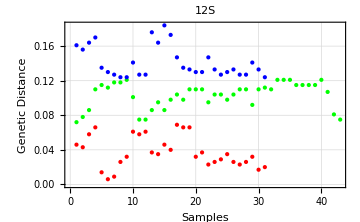

```mathematica
PlotCluster[MySort[clstrnematode12S],"12S"]
```

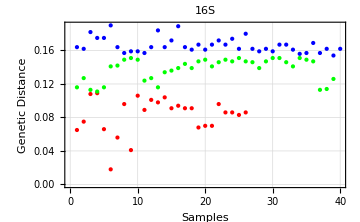

```mathematica
PlotCluster[MySort[clstrnematode16S],"16S"]
```

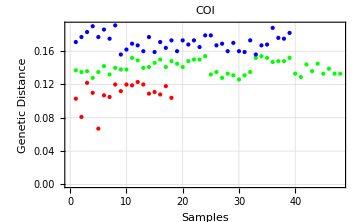

```mathematica
PlotCluster[MySort[clstrnematodeCOI],"COI"]
```

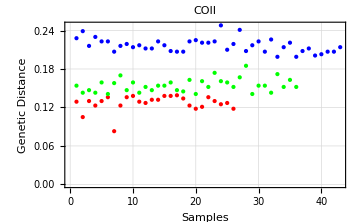

```mathematica
PlotCluster[MySort[clstrnematodeCOII],"COII"]
```

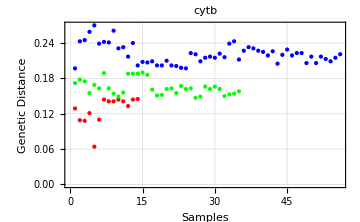

```mathematica
PlotCluster[MySort[clstrnematodecytb],"cytb"]
```

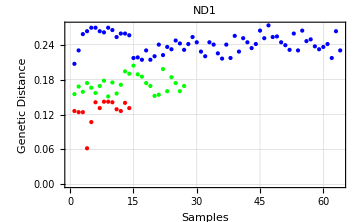

```mathematica
PlotCluster[MySort[clstrnematodeND],"ND1"]
```

```mathematica
FindClusters[nematode12S,3,Method->"KMeans"]
```

{{0.046,0.043,0.058,0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02},{0.072,0.078,0.086,0.11,0.115,0.112,0.118,0.118,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.107,0.081,0.075},{0.161,0.156,0.164,0.17,0.135,0.13,0.127,0.124,0.124,0.141,0.127,0.127,0.176,0.164,0.184,0.173,0.147,0.135,0.133,0.13,0.13,0.147,0.133,0.127,0.13,0.133,0.127,0.127,0.141,0.133,0.124}}

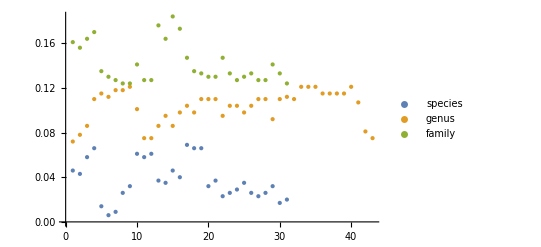

```mathematica
ListPlot[FindClusters[nematode12S,3,Method->"KMeans"],PlotLegends->{species,genus,family},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.046,0.043,0.058,0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

0.0375806

```mathematica
StandardDeviation[{0.046,0.043,0.058,0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

0.0180403

```mathematica
MinMax[{0.046,0.043,0.058,0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

{0.006,0.069}

```mathematica
Mean[{0.072,0.078,0.086,0.11,0.115,0.112,0.118,0.118,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.107,0.081,0.075}]
```

0.103116

```mathematica
StandardDeviation[{0.072,0.078,0.086,0.11,0.115,0.112,0.118,0.118,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.107,0.081,0.075}]
```

0.0146226

```mathematica
MinMax[{0.072,0.078,0.086,0.11,0.115,0.112,0.118,0.118,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.107,0.081,0.075}]
```

{0.072,0.121}

```mathematica
Mean[{0.161,0.156,0.164,0.17,0.135,0.13,0.127,0.124,0.124,0.141,0.127,0.127,0.176,0.164,0.184,0.173,0.147,0.135,0.133,0.13,0.13,0.147,0.133,0.127,0.13,0.133,0.127,0.127,0.141,0.133,0.124}]
```

0.14129

```mathematica
StandardDeviation[{0.161,0.156,0.164,0.17,0.135,0.13,0.127,0.124,0.124,0.141,0.127,0.127,0.176,0.164,0.184,0.173,0.147,0.135,0.133,0.13,0.13,0.147,0.133,0.127,0.13,0.133,0.127,0.127,0.141,0.133,0.124}]
```

0.0178385

```mathematica
MinMax[{0.161,0.156,0.164,0.17,0.135,0.13,0.127,0.124,0.124,0.141,0.127,0.127,0.176,0.164,0.184,0.173,0.147,0.135,0.133,0.13,0.13,0.147,0.133,0.127,0.13,0.133,0.127,0.127,0.141,0.133,0.124}]
```

{0.124,0.184}

```mathematica
FindClusters[nematode16S,3,Method->"KMeans"]
```

{{0.072,0.078,0.086,0.066,0.11,0.115,0.112,0.101,0.075,0.075,0.069,0.086,0.095,0.086,0.066,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.11,0.112,0.11,0.115,0.115,0.115,0.115,0.107,0.081,0.066,0.075},{0.043,0.058,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02},{0.161,0.156,0.164,0.17,0.135,0.13,0.127,0.124,0.124,0.141,0.127,0.127,0.176,0.164,0.184,0.173,0.147,0.135,0.133,0.13,0.13,0.147,0.133,0.127,0.118,0.118,0.13,0.121,0.133,0.127,0.127,0.121,0.121,0.121,0.141,0.121,0.133,0.124}}

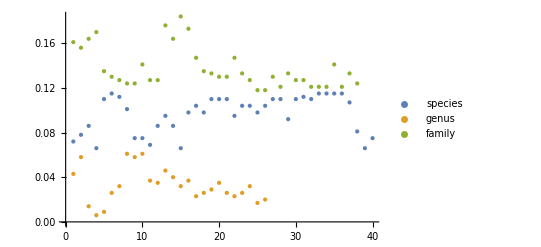

```mathematica
ListPlot[FindClusters[nematode16S,3,Method->"KMeans"],PlotLegends->{species,genus,family},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.072,0.078,0.086,0.066,0.11,0.115,0.112,0.101,0.075,0.075,0.069,0.086,0.095,0.086,0.066,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.11,0.112,0.11,0.115,0.115,0.115,0.115,0.107,0.081,0.066,0.075}]
```

0.0965

```mathematica
StandardDeviation[{0.072,0.078,0.086,0.066,0.11,0.115,0.112,0.101,0.075,0.075,0.069,0.086,0.095,0.086,0.066,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.11,0.112,0.11,0.115,0.115,0.115,0.115,0.107,0.081,0.066,0.075}]
```

0.0163957

```mathematica
MinMax[{0.072,0.078,0.086,0.066,0.11,0.115,0.112,0.101,0.075,0.075,0.069,0.086,0.095,0.086,0.066,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.11,0.112,0.11,0.115,0.115,0.115,0.115,0.107,0.081,0.066,0.075}]
```

{0.066,0.115}

```mathematica
Mean[{0.043,0.058,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

0.0327692

```mathematica
StandardDeviation[{0.043,0.058,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

0.015074

```mathematica
MinMax[{0.043,0.058,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

{0.006,0.061}

```mathematica
Mean[{0.161,0.156,0.164,0.17,0.135,0.13,0.127,0.124,0.124,0.141,0.127,0.127,0.176,0.164,0.184,0.173,0.147,0.135,0.133,0.13,0.13,0.147,0.133,0.127,0.118,0.118,0.13,0.121,0.133,0.127,0.127,0.121,0.121,0.121,0.141,0.121,0.133,0.124}]
```

0.137395

```mathematica
StandardDeviation[{0.161,0.156,0.164,0.17,0.135,0.13,0.127,0.124,0.124,0.141,0.127,0.127,0.176,0.164,0.184,0.173,0.147,0.135,0.133,0.13,0.13,0.147,0.133,0.127,0.118,0.118,0.13,0.121,0.133,0.127,0.127,0.121,0.121,0.121,0.141,0.121,0.133,0.124}]
```

0.0180937

```mathematica
MinMax[{0.161,0.156,0.164,0.17,0.135,0.13,0.127,0.124,0.124,0.141,0.127,0.127,0.176,0.164,0.184,0.173,0.147,0.135,0.133,0.13,0.13,0.147,0.133,0.127,0.118,0.118,0.13,0.121,0.133,0.127,0.127,0.121,0.121,0.121,0.141,0.121,0.133,0.124}]
```

{0.118,0.184}

```mathematica
FindClusters[nematodeCOI,3,Method->"KMeans"]
```

{{0.043,0.058,0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02},{0.078,0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075},{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}}

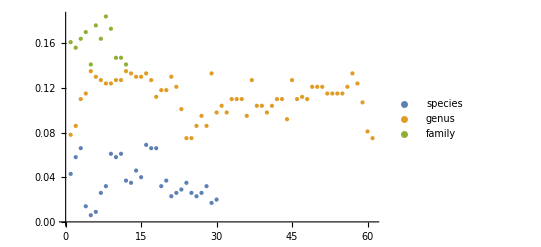

```mathematica
ListPlot[FindClusters[nematodeCOI,3,Method->"KMeans"],PlotLegends->{species,genus,family},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.043,0.058,0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

0.0373

```mathematica
StandardDeviation[{0.043,0.058,0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

0.0182797

```mathematica
MinMax[{0.043,0.058,0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

{0.006,0.069}

```mathematica
Mean[{0.078,0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075}]
```

0.11177

```mathematica
StandardDeviation[{0.078,0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075}]
```

0.0166687

```mathematica
MinMax[{0.078,0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075}]
```

{0.075,0.135}

```mathematica
Mean[{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}]
```

0.160333

```mathematica
StandardDeviation[{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}]
```

0.01417

```mathematica
MinMax[{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}]
```

{0.141,0.184}

```mathematica
FindClusters[nematodeCOII,3,Method->"KMeans"]
```

{{0.058,0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02},{0.078,0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075},{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}}

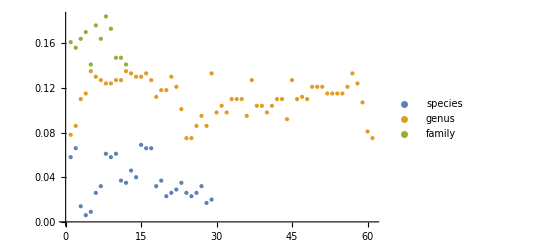

```mathematica
ListPlot[FindClusters[nematodeCOII,3,Method->"KMeans"],PlotLegends->{species,genus,family},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.058,0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

0.0371034

```mathematica
StandardDeviation[{0.058,0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

0.018571

```mathematica
MinMax[{0.058,0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

{0.006,0.069}

```mathematica
Mean[{0.078,0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075}]
```

0.11177

```mathematica
StandardDeviation[{0.078,0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075}]
```

0.0166687

```mathematica
MinMax[{0.078,0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075}]
```

{0.075,0.135}

```mathematica
Mean[{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}]
```

0.160333

```mathematica
StandardDeviation[{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}]
```

0.01417

```mathematica
MinMax[{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}]
```

{0.141,0.184}

```mathematica
FindClusters[nematodecytb,3,Method->"KMeans"]
```

{{0.078,0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075},{0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02},{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}}

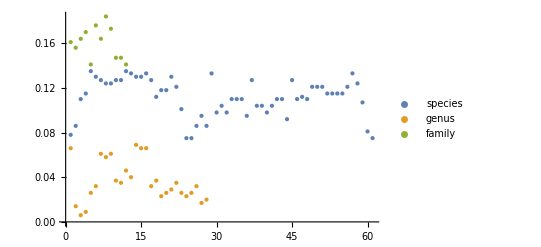

```mathematica
ListPlot[FindClusters[nematodecytb,3,Method->"KMeans"],PlotLegends->{species,genus,family},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.078,0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075}]
```

0.11177

```mathematica
StandardDeviation[{0.078,0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075}]
```

0.0166687

```mathematica
MinMax[{0.078,0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075}]
```

{0.075,0.135}

```mathematica
Mean[{0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

0.0363571

```mathematica
StandardDeviation[{0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

0.0184636

```mathematica
MinMax[{0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

{0.006,0.069}

```mathematica
Mean[{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}]
```

0.160333

```mathematica
StandardDeviation[{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}]
```

0.01417

```mathematica
MinMax[{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}]
```

{0.141,0.184}

```mathematica
FindClusters[nematodeND,3,Method->"KMeans"]
```

{{0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075},{0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02},{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}}

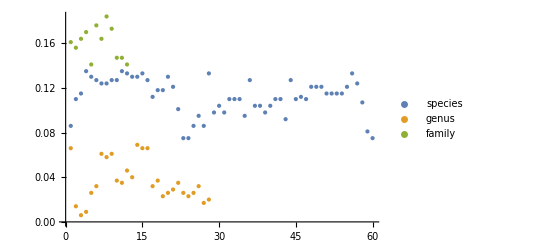

```mathematica
ListPlot[FindClusters[nematodeND,3,Method->"KMeans"],PlotLegends->{species,genus,family},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075}]
```

0.112333

```mathematica
StandardDeviation[{0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075}]
```

0.0162143

```mathematica
MinMax[{0.086,0.11,0.115,0.135,0.13,0.127,0.124,0.124,0.127,0.127,0.135,0.133,0.13,0.13,0.133,0.127,0.112,0.118,0.118,0.13,0.121,0.101,0.075,0.075,0.086,0.095,0.086,0.133,0.098,0.104,0.098,0.11,0.11,0.11,0.095,0.127,0.104,0.104,0.098,0.104,0.11,0.11,0.092,0.127,0.11,0.112,0.11,0.121,0.121,0.121,0.115,0.115,0.115,0.115,0.121,0.133,0.124,0.107,0.081,0.075}]
```

{0.075,0.135}

```mathematica
Mean[{0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

0.0363571

```mathematica
StandardDeviation[{0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

0.0184636

```mathematica
MinMax[{0.066,0.014,0.006,0.009,0.026,0.032,0.061,0.058,0.061,0.037,0.035,0.046,0.04,0.069,0.066,0.066,0.032,0.037,0.023,0.026,0.029,0.035,0.026,0.023,0.026,0.032,0.017,0.02}]
```

{0.006,0.069}

```mathematica
Mean[{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}]
```

0.160333

```mathematica
StandardDeviation[{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}]
```

0.01417

```mathematica
MinMax[{0.161,0.156,0.164,0.17,0.141,0.176,0.164,0.184,0.173,0.147,0.147,0.141}]
```

{0.141,0.184}